```mathematica
Derivative[f[x_] := Sin[x] + x^2][f'[x]]
```

(2 x+Cos[x])^(Null)

```mathematica
The built-in function Reduce provides the functionality previously found inAlgebra`InequalitySolve`.
```

```mathematica
Instead ofInequalitySolve[expr,vars]you should use Reduce[expr,vars,Reals]:
```

```mathematica
Списки минимизации и максимизации доходности с указанием значения,достигаемого при минимальном или максимальном значении,вместе с правилами,определяющими,где происходит минимальное или максимальное значение.
```

```mathematica
Minimize[x^2-3x+6,x]
```

{15/4,{x→3/2}}

```mathematica
Maximize[{5 x y-x^4-y^4,x+y==1},{x,y}]
```

{9/8,{x→1/2,y→1/2}}

```mathematica
Table[x,10]
```

{x,x,x,x,x,x,x,x,x,x}

```mathematica
Table[10i+j,{i,4},{j,3}]
```

{{11,12,13},{21,22,23},{31,32,33},{41,42,43}}

```mathematica
MatrixForm[%]
```

```mathematica
({{11, 12, 13}, {21, 22, 23}, {31, 32, 33}})
```

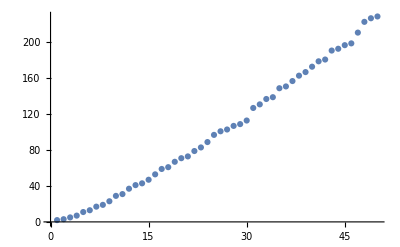

```mathematica
ListPlot[Table[Prime[i],{i,50}]]
```

```mathematica
Column[Table[Prime[i],{i,5}]]
```

2
3
5
7
11

```mathematica
Length[{a,b,c,d}]
```

4

```mathematica
Length[<||>]
```

0

```mathematica
Length[<|1->2, 3->4|>]
```

2

```mathematica
Flatten[{{a,b},{c,{d},e},{f,{g,h}}}]
```

{a,b,c,d,e,f,g,h}

```mathematica
Flatten[{{a,b},{c,{d},e},{f,{g,h}}},1]
```

{a,b,c,{d},e,f,{g,h}}

```mathematica
Flatten[{{a,b},{c,{d},e},{f,{g,h}}},2]
```

{a,b,c,d,e,f,g,h}

```mathematica
Flatten[{{a,b},{c,{d},e},{f,{g,h}}},0]
```

{{a,b},{c,{d},e},{f,{g,h}}}

```mathematica
IdentityMatrix[3]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Det[({{Subscript[a, 1,1], Subscript[a, 1,2]}, {Subscript[a, 2,1], Subscript[a, 2,2]}})]
```

-a_(1,2) a_(2,1)+a_(1,1) a_(2,2)

```mathematica
Det[({{Subscript[a, 1,1], Subscript[a, 1,2], Subscript[a, 1,3]}, {Subscript[a, 2,1], Subscript[a, 2,2], Subscript[a, 2,3]}, {Subscript[a, 3,1], Subscript[a, 3,2], Subscript[a, 3,3]}})]
```

-a_(1,3) a_(2,2) a_(3,1)+a_(1,2) a_(2,3) a_(3,1)+a_(1,3) a_(2,1) a_(3,2)-a_(1,1) a_(2,3) a_(3,2)-a_(1,2) a_(2,1) a_(3,3)+a_(1,1) a_(2,2) a_(3,3)

```mathematica
Det[{{1,2,3},{4,5,6},{7,8,9}}]
```

0

```mathematica
The trace of a matrix is the sum of the diagonal elements:
```

```mathematica
Tr[{{1,2,3},{4,5,6},{7,8,9}}]
```

15

```mathematica
MatrixRank[{{1,2,3},{4,5,6},{7,8,9}}]
```

2

```mathematica
Transpose[{{a,b,c},{x,y,z}}]
```

{{a,x},{b,y},{c,z}}

```mathematica
Inverse[({{1, 2, 3}, {4, 2, 2}, {5, 1, 7}})]
```

{{-2/7,11/42,1/21},{3/7,4/21,-5/21},{1/7,-3/14,1/7}}

```mathematica
Matrix product:
```

```mathematica
{{a,b},{c,d}} . {{r,s},{t,u}}
```

{{a r+b t,a s+b u},{c r+d t,c s+d u}}

```mathematica
Abs absolute value of the real or complex numberz
```

```mathematica
Abs[-4]
```

4

```mathematica
Abs[1.4+2.3I]
```

2.69258

```mathematica
Abs[{-2,-1,0,1,2}]
```

{2,1,0,1,2}

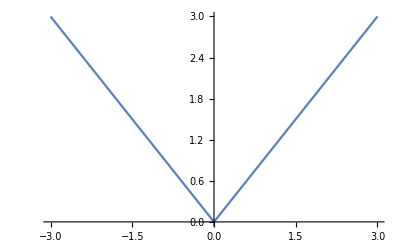

```mathematica
Plot[Abs[x],{x,-3,3}]
```

```mathematica
Max[9,2]
```

9

```mathematica
Max[{4,1,7,2}]
```

7

```mathematica
Expand polynomial expressions:
```

```mathematica
Expand[(1+x)^10]
```

1+10 x+45 x^2+120 x^3+210 x^4+252 x^5+210 x^6+120 x^7+45 x^8+10 x^9+x^10

```mathematica
Factor, как я поняла, это разложить на множетели
```

```mathematica
Factor[1+2x+x^2]
```

(1+x)^2

```mathematica
Factor[x^10-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

```mathematica
Factor[x^10-y^10]
```

(x-y) (x+y) (x^4-x^3 y+x^2 y^2-x y^3+y^4) (x^4+x^3 y+x^2 y^2+x y^3+y^4)

```mathematica
Factor[x^10-1,Modulus->2]
```

(1+x)^2 (1+x+x^2+x^3+x^4)^2

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

```mathematica
Simplify[Sqrt[x^2]]
```

√(x^2)

```mathematica
Simplify[Sqrt[x^2],x>0]
```

x

```mathematica
Simplify[Sqrt[x^2],x<0]
```

-x

```mathematica
Simplify[Sqrt[x^2], Element[x, Reals]]
```

Abs[x]

```mathematica
N[1/7]
```

0.142857

```mathematica
N[1/7,50]
```

0.14285714285714285714285714285714285714285714285714

```mathematica
Chop replaces approximate real numbers inexprthat are close to zero by the exact integer0
```

```mathematica
InverseFourier[Fourier[{2,1,1,0,0,0}]]
```

{2.,1.,1.,0.,0.,0.}

```mathematica
Chop[%]
```

{2.,1.,1.,0,0,0}

```mathematica
Chop[1.,10., 0.00000000000000002, 4.]
```

Chop::argt: Chop called with 4 arguments; 1 or 2 arguments are expected.

Chop[1.,10.,2.×10^-17,4.]

```mathematica
2+2==4
```

True

```mathematica
x^2==1+x
```

x^2==1+x

```mathematica
Solve[%,x]
```

{{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

```mathematica
Do[Print[n^2],{n,4}]
```

1

4

9

16

```mathematica
Do[Print[n],{n,-3,5,2}]
```

-3

-1

1

3

5

```mathematica
Do[Print[RandomInteger[10]],4]
```

1

3

0

9

```mathematica
n=1;While[n<4,Print[n];n++]
```

1

2

3

```mathematica
x=-2;
If[x<0,y=-x,y=x];y
```

2

```mathematica
y=If[x<0,-x,x]
```

2

```mathematica
a=2;Which[a==1,x,a==2,b]
```

b